```mathematica
opts = {BaseStyle->{FontSize->15}, Frame->True, PlotStyle->Black, ImageSize->600};
SetOptions[{Plot,ListPlot,ListLogPlot}, opts];
```

```mathematica
mec2N = 0.510998910 10^6;
```

## ibs_linac

```mathematica
workdir = NotebookDirectory[]<>"LCLS2/"
```

/Volumes/accuser/cem52/linux_lib/bsim/ibs_linac/test/LCLS2/

```mathematica
IBSData[file_]:=Module[{},
rdat = Import[file, "Table"];
ix1 = Position[rdat, "BEGIN_DATA"]⟦1,1⟧ ;
ix2 = Position[rdat, "END_DATA"]⟦1,1⟧ ;
header=rdat⟦ix1+1⟧;
units = rdat⟦ix1+2⟧;
rdat⟦ix1+3;;ix2-1⟧
];
```

```mathematica
Table[{i, header⟦i⟧}, {i,1,Length[header]}]
```

{{1,s},{2,gamma},{3,norm_emit_a},{4,norm_emit_b},{5,sigma_z/c},{6,sigma_E},{7,demit_a},{8,demit_b},{9,dsigma_E}}

```mathematica
units
```

{m,1,mm-mrad,mm-mrad,fs,eV,mm-mrad,mm-mrad,eV}

```mathematica
dat =IBSData[ workdir<>"ibs.out"];
```

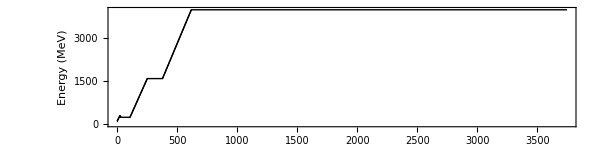

```mathematica
energyG=ListPlot[{#⟦1⟧, 10^-6 mec2N#⟦2⟧}&/@dat, FrameLabel->{"s (m)", "Energy (MeV)"}, Joined->True , AspectRatio->1/4]
```

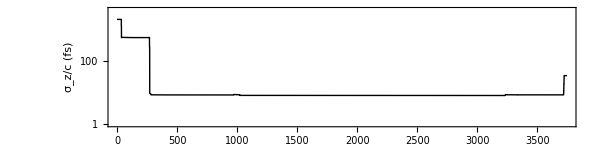

```mathematica
sigmazG=ListLogPlot[{#⟦1⟧, #⟦5⟧}&/@dat, FrameLabel->{"s (m)", "σ_z/c (fs)"}, Joined->True , AspectRatio->1/4, PlotRange->{1,4000}]
```

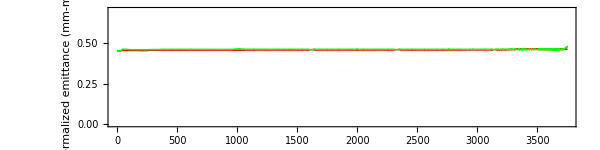

```mathematica
c1=Red;
c2=Green;
emitG =ListPlot[{
{#⟦1⟧, #⟦3⟧}&/@dat,
{#⟦1⟧, #⟦4⟧}&/@dat}, FrameLabel->{"s (m)", "normalized emittance\n(mm-mrad)"}, Joined->True , AspectRatio->1/4, PlotRange->{0,0.7}, PlotStyle->{c1,c2}]
```

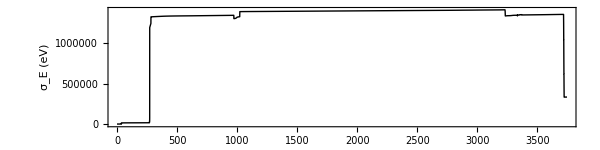

```mathematica
sigmaEG=ListPlot[{#⟦1⟧, #⟦6⟧}&/@dat, FrameLabel->{"s (m)", "σ_E (eV)"}, Joined->True , AspectRatio->1/4,PlotRange->{0,All}]
```

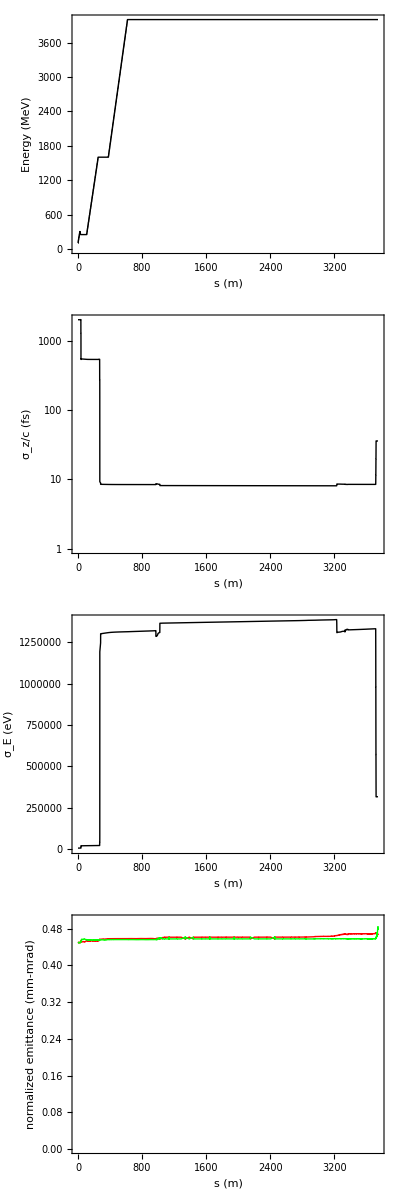

```mathematica
isize = 800;
ipad={{100,10},{50,10}};
gout = Grid[{
{Show[energyG, ImageSize->isize, ImagePadding->ipad]},
{Show[sigmazG, ImageSize->isize, ImagePadding->ipad]},
{Show[sigmaEG, ImageSize->isize, ImagePadding->ipad]},
{Show[emitG, ImageSize->isize, ImagePadding->ipad]}}]
```

```mathematica
(*Export[workdir<>"ibs.pdf", gout]
```

```mathematica
(*headerstrings = StringSplit[ Import[outfile, "String"], "\n"]⟦1;;17⟧*)
```

## Comparison

```mathematica
dat0 =IBSData[ workdir<>"ibs_short0.out"];
dat1 =IBSData[ workdir<>"ibs_short1.out"];
dat2 =IBSData[ workdir<>"ibs_short2.out"];
```

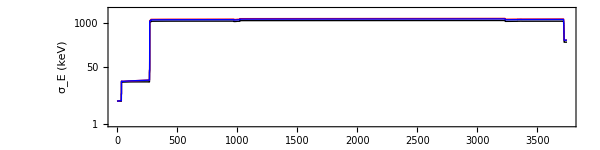

```mathematica
myf = {#⟦1⟧, 10^-3#⟦6⟧}&;
compG1 = ListLogPlot[{
(myf /@dat0),
(myf /@dat1),
(myf /@dat2)},
 FrameLabel->{"s (m)", "σ_E (keV)"}, Joined->True , AspectRatio->1/4,PlotRange->{1, 2500}, PlotStyle->{Black,Red, Blue}]
```

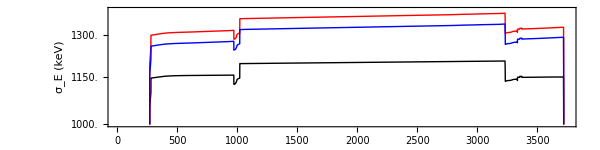

```mathematica
myf = {#⟦1⟧, 10^-3#⟦6⟧}&;
compG1zoom= ListLogPlot[{
(myf /@dat0),
(myf /@dat1),
(myf /@dat2)},
 FrameLabel->{"s (m)", "σ_E (keV)"}, Joined->True , AspectRatio->1/4,PlotRange->{1000, 1400}, PlotStyle->{Black,Red, Blue}]
```

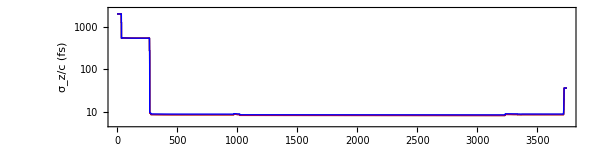

```mathematica
myf = {#⟦1⟧, #⟦5⟧}&;
compG2 = ListLogPlot[{
(myf /@dat0),
(myf /@dat1),
(myf /@dat2)},
 FrameLabel->{"s (m)", "σ_z/c (fs)"}, Joined->True , AspectRatio->1/4,PlotRange->{5, 2500}, PlotStyle->{Black,Red, Blue}]
```

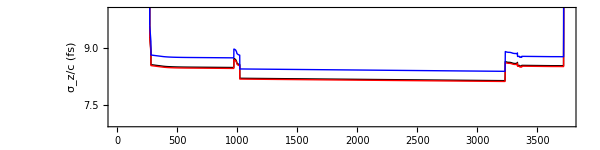

```mathematica
myf = {#⟦1⟧, #⟦5⟧}&;
compG2zoom = ListPlot[{
(myf /@dat0),
(myf /@dat1),
(myf /@dat2)},
 FrameLabel->{"s (m)", "σ_z/c (fs)"}, Joined->True , AspectRatio->1/4,PlotRange->{7,10}, PlotStyle->{Black,Red, Blue}]
```

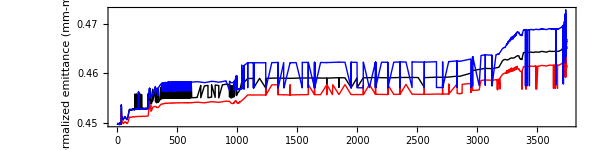

```mathematica
myf = {#⟦1⟧, #⟦3⟧}&;
compG3 = ListLogPlot[{
(myf /@dat0),
(myf /@dat1),
(myf /@dat2)},
 FrameLabel->{"s (m)", "normalized emittance\n(mm-mrad)"}, Joined->True , AspectRatio->1/4,PlotRange->{0,0.5}, PlotStyle->{Black,Red, Blue}]
```

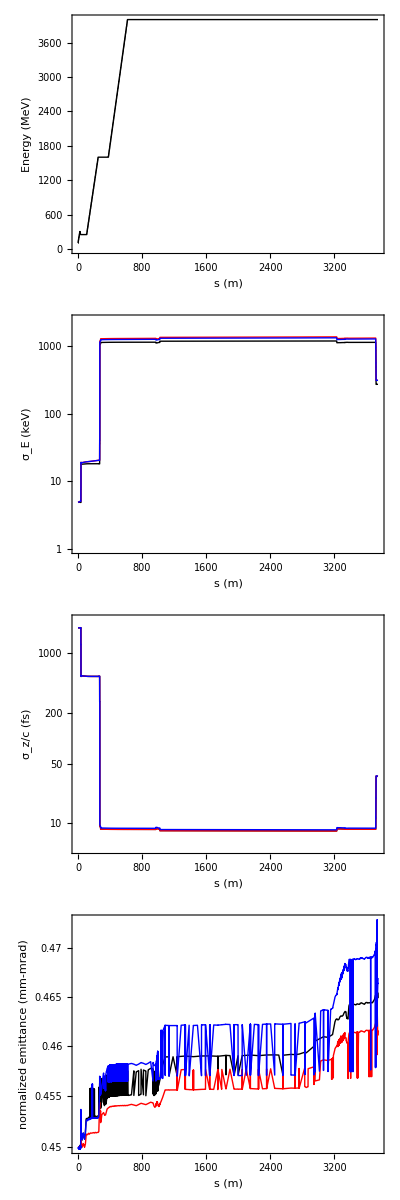

```mathematica
isize = 800;
ipad={{100,10},{50,10}};
gout1 = Grid[{
{Show[energyG, ImageSize->isize, ImagePadding->ipad]},
{Show[compG1, ImageSize->isize, ImagePadding->ipad]},
{Show[compG2 , ImageSize->isize, ImagePadding->ipad]},
{Show[compG3 , ImageSize->isize, ImagePadding->ipad]}}]
```

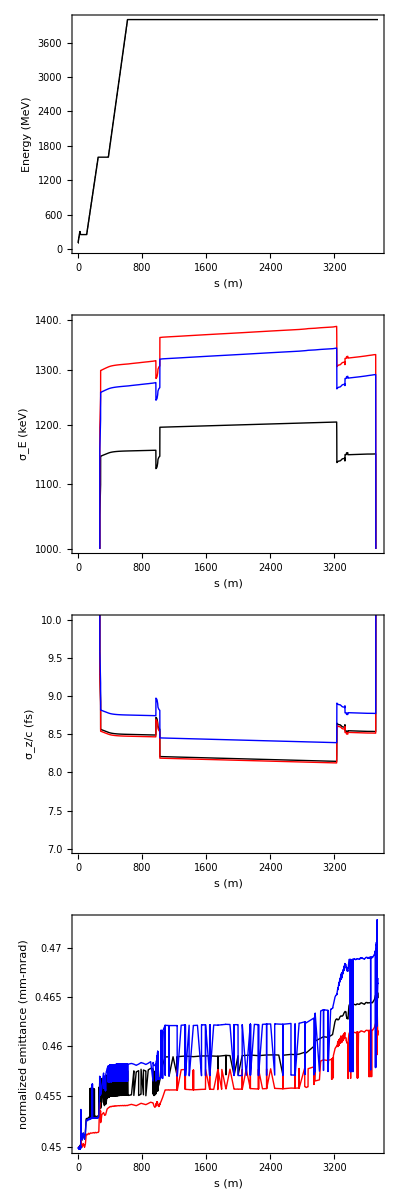

```mathematica
isize = 800;
ipad={{100,10},{50,10}};
gout2 = Grid[{
{Show[energyG, ImageSize->isize, ImagePadding->ipad]},
{Show[compG1zoom, ImageSize->isize, ImagePadding->ipad]},
{Show[compG2zoom , ImageSize->isize, ImagePadding->ipad]},
{Show[compG3 , ImageSize->isize, ImagePadding->ipad]}}]
```

```mathematica
Export[workdir<>"ibs_comparison1.pdf", gout1]
```

/Volumes/accuser/cem52/linux_lib/bsim/ibs_linac/test/LCLS2/ibs_comparison1.pdf

```mathematica
Export[workdir<>"ibs_comparison2.pdf", gout2]
```

/Volumes/accuser/cem52/linux_lib/bsim/ibs_linac/test/LCLS2/ibs_comparison2.pdf